```mathematica
(* ::Section::*)(*Root cell*)
ClearAll["Global`*"];
$HistoryLength=0;

projectRoot=ExpandFileName@FileNameJoin[{NotebookDirectory[],".."}];

If[!DirectoryQ[projectRoot],Print["[ERROR] Project root not found: ",projectRoot];
Abort[];];

srcRoot=FileNameJoin[{projectRoot,"src","CVTPulley","Kernel"}];
notebooksRoot=FileNameJoin[{projectRoot,"notebooks"}];
testsRoot=FileNameJoin[{projectRoot,"tests"}];
examplesRoot=FileNameJoin[{projectRoot,"examples"}];
docsRoot=FileNameJoin[{projectRoot,"docs"}];
outputRoot=FileNameJoin[{projectRoot,"output"}];

SetDirectory[projectRoot];

Print["Project root:   ",projectRoot];
Print["Notebook dir:   ",NotebookDirectory[]];
Print["Kernel src dir: ",srcRoot];
```

Project root:   C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\MATEMATIKA\r - kontinuirani prijenos\clanak za casopis\Computational Mathematics and Modeling\cvt-symmetry-wm

Notebook dir:   C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\MATEMATIKA\r - kontinuirani prijenos\clanak za casopis\Computational Mathematics and Modeling\cvt-symmetry-wm\notebooks\

Kernel src dir: C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\MATEMATIKA\r - kontinuirani prijenos\clanak za casopis\Computational Mathematics and Modeling\cvt-symmetry-wm\src\CVTPulley\Kernel

```mathematica
(* ::Section::*)(*Loader cell*)
wlFiles={"TypesAndValidation.wl","Geometry.wl","BeltLength.wl","RootFinding.wl","ImplicitMap.wl","Symmetrization.wl"};

wlPaths=FileNameJoin[{srcRoot,#}]&/@wlFiles;

missingFiles=Select[wlPaths,!FileExistsQ[#]&];

If[missingFiles=!={},Print["[ERROR] Missing .wl files:"];
Scan[Print["   - ",#]&,missingFiles];
Abort[];];

Scan[Function[path,Get[path];
Print["[LOADED] ",FileNameTake[path]]],wlPaths];
Print[""];
Print["Loaded ",Length[wlPaths]," file(s) from:"];
Print[srcRoot];

loadedSymbols=<|"MakeParameters"->NameQ["CVTPulley`TypesAndValidation`MakeParameters"],"GeometrySummary"->NameQ["CVTPulley`Geometry`GeometrySummary"],"BeltLength"->NameQ["CVTPulley`BeltLength`BeltLength"]|>;

Print[""];
Print["Symbol check:"];
KeyValueMap[Print["   ",#1," -> ",If[#2,"OK","MISSING"]]&,loadedSymbols];
```

[LOADED] TypesAndValidation.wl

[LOADED] Geometry.wl

[LOADED] BeltLength.wl

[LOADED] RootFinding.wl

[LOADED] ImplicitMap.wl

[LOADED] Symmetrization.wl

Loaded 6 file(s) from:

C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\MATEMATIKA\r - kontinuirani prijenos\clanak za casopis\Computational Mathematics and Modeling\cvt-symmetry-wm\src\CVTPulley\Kernel

Symbol check:

MakeParameters -> OK

GeometrySummary -> OK

BeltLength -> OK

```mathematica
(* ::Section::*)(*Article parameters*)paramsArticle=CVTPulley`TypesAndValidation`MakeParameters[<|"rMin"->10.0,"rMax"->30.0,"d"->70.0,"nGrid"->100,"epsSym"->10^-6,"epsBis"->10^-12,"maxSymIter"->200,"maxBisIter"->200,"workingPrecision"->MachinePrecision,"beltLength"->Missing["ToBeComputed"]|>];

paramsArticle=CVTPulley`BeltLength`SetReferenceBeltLength[paramsArticle];

Print["Article L0 (corrected) = ",N[paramsArticle["beltLength"],12]];
```

ValidateParameters::warnprec: Warning: workingPrecision is MachinePrecision while epsBis = 1/1000000000000; high-accuracy bisection may later require a higher WorkingPrecision.

Article L0 (corrected) = 271.418

```mathematica
(* ::Section::*)(*Corrected Table 1*)pair23=CVTPulley`Symmetrization`IterateSymmetricPair[23,paramsArticle,"StoreHistory"->True,"ImplicitStoreHistory"->False];

hist23=CVTPulley`Symmetrization`PairIterationTable[pair23];

table1Corrected=Table[<|"n"->hist23[[k,"Iteration"]],"r_n(t_i)"->N[hist23[[k,"rLeft"]],10],"R_n(t_i)"->N[hist23[[k,"RLeft"]],10],"r_n(1-t_i)"->N[hist23[[k,"rRight"]],10],"R_n(1-t_i)"->N[hist23[[k,"RRight"]],10],"eps_i"->N[hist23[[k,"MaxCrossError"]],12]|>,{k,Length[hist23]}];

table1Corrected//TableForm
```

<|n→1,r_n(t_i)→14.6,R_n(t_i)→26.5776,r_n(1-t_i)→25.4,R_n(1-t_i)→16.0319,eps_i→1.43193|>
<|n→2,r_n(t_i)→15.316,R_n(t_i)→25.996,r_n(1-t_i)→25.9888,R_n(1-t_i)→15.3246,eps_i→0.00867869|>
<|n→3,r_n(t_i)→15.3203,R_n(t_i)→25.9924,r_n(1-t_i)→25.9924,R_n(1-t_i)→15.3203,eps_i→3.18809×10^-7|>

```mathematica
table1Headers={"n","r_n(t_i)","R_n(t_i)","r_n(1-t_i)","R_n(1-t_i)","eps_i"};

table1Rows=table1Corrected/. assoc_Association:>Values[assoc];

Export[FileNameJoin[{outputRoot,"tables","Table1_corrected.xlsx"}],Prepend[table1Rows,table1Headers]]
```

C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\MATEMATIKA\r - kontinuirani prijenos\clanak za casopis\Computational Mathematics and Modeling\cvt-symmetry-wm\output\tables\Table1_corrected.xlsx

```mathematica
(* ::Section::*)(*Corrected Table 2*)
midArticle=CVTPulley`Symmetrization`IterateMidpoint[paramsArticle,"StoreHistory"->True,"ImplicitStoreHistory"->False];

midHist=CVTPulley`Symmetrization`PairIterationTable[midArticle];

table2Corrected=Table[<|"n"->midHist[[k,"Iteration"]],"r_n(0.5)"->N[midHist[[k,"r"]],10],"R_n(0.5)"->N[midHist[[k,"R"]],10],"eps"->N[midHist[[k,"Error"]],12]|>,{k,Length[midHist]}];

table2Corrected//TableForm
```

<|n→1,r_n(0.5)→20.,R_n(0.5)→21.8166,eps→1.81659|>
<|n→2,r_n(0.5)→20.9083,R_n(0.5)→20.9233,eps→0.0150059|>
<|n→3,r_n(0.5)→20.9158,R_n(0.5)→20.9158,eps→1.02395×10^-6|>
<|n→4,r_n(0.5)→20.9158,R_n(0.5)→20.9158,eps→1.42109×10^-13|>

```mathematica
Export[FileNameJoin[{outputRoot,"tables","Table2_corrected.xlsx"}],Prepend[(Values/@(Normal/@table2Corrected)),Keys[Normal[table2Corrected[[1]]]]]]
```

C:\Users\User\OneDrive - Veleučilište Velika Gorica\RADNO_tekstovi\MATEMATIKA\r - kontinuirani prijenos\clanak za casopis\Computational Mathematics and Modeling\cvt-symmetry-wm\output\tables\Table2_corrected.xlsx

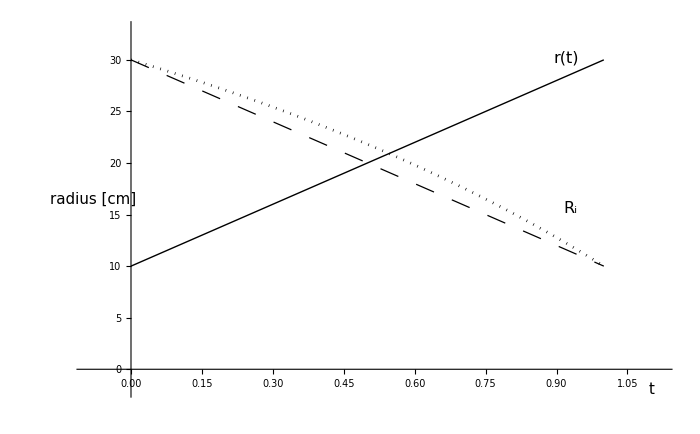

```mathematica
(* ::Section::*)(*Article-style Figure 2*)tGrid2=mapDataArticle["tGrid"];
rGrid2=mapDataArticle["rGrid"];
RGrid2=mapDataArticle["RGrid"];

rMin2=paramsArticle["rMin"];
rMax2=paramsArticle["rMax"];

linearComparison=Table[{t,rMax2-t (rMax2-rMin2)},{t,tGrid2}];

fig2Article=Show[{ListLinePlot[Transpose[{tGrid2,rGrid2}],PlotStyle->Directive[Black,AbsoluteThickness[1.0]],InterpolationOrder->1],ListLinePlot[Transpose[{tGrid2,RGrid2}],PlotStyle->Directive[Black,AbsoluteThickness[2],Dotted],InterpolationOrder->1],ListLinePlot[linearComparison,PlotStyle->Directive[Black,AbsoluteThickness[0.9],Dashing[{0.02,0.02}]],InterpolationOrder->1]},Axes->True,Frame->False,AxesOrigin->{0,0},AxesStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,12],PlotRange->{{-0.09,1.12},{-2,33}},ImageSize->700,AspectRatio->0.62,PlotRangePadding->Scaled[0.02],Epilog->{Inset[Style["r(t)",16,Black,Italic],{0.92,30.2}],Inset[Style[Subscript[Style["R",Italic],"i"],16,Black],{0.93,15.6}],Inset[Style["t",15,Black,Italic],{1.1,-2}],Rotate[Inset[Style["radius [cm]",15,Black],{-0.08,16.5}],Pi/2]}];

fig2Article

Export[FileNameJoin[{outputRoot,"figures","Figure2_article_style.png"}],fig2Article,ImageResolution->300];

Export[FileNameJoin[{outputRoot,"figures","Figure2_article_style.pdf"}],fig2Article];
```

```mathematica
(* ::Section::*)(*Grid and profiles for Figure 4*)
symArticle=CVTPulley`Symmetrization`SymmetrizationData[paramsArticle,"StoreHistory"->False,"ImplicitStoreHistory"->False];

If[FailureQ[symArticle],Print["[ERROR] SymmetrizationData failed."];
Print[symArticle];
Abort[],Print["[OK] Full symmetrization computed."]];

profilesArticle=CVTPulley`Symmetrization`BuildSymmetricDiscreteProfiles[symArticle];

If[FailureQ[profilesArticle],Print["[ERROR] BuildSymmetricDiscreteProfiles failed."];
Print[profilesArticle];
Abort[],Print["[OK] Final profiles built."]];

tGrid4=profilesArticle["tGrid"];
rGrid4=profilesArticle["rGrid"];
RGrid4=profilesArticle["RGrid"];

Print[""];
Print["Profile sizes:"];
Print["   Length[tGrid4] = ",Length[tGrid4]];
Print["   Length[rGrid4] = ",Length[rGrid4]];
Print["   Length[RGrid4] = ",Length[RGrid4]];
```

[OK] Full symmetrization computed.

[OK] Final profiles built.

Profile sizes:

Length[tGrid4] = 101

Length[rGrid4] = 101

Length[RGrid4] = 101

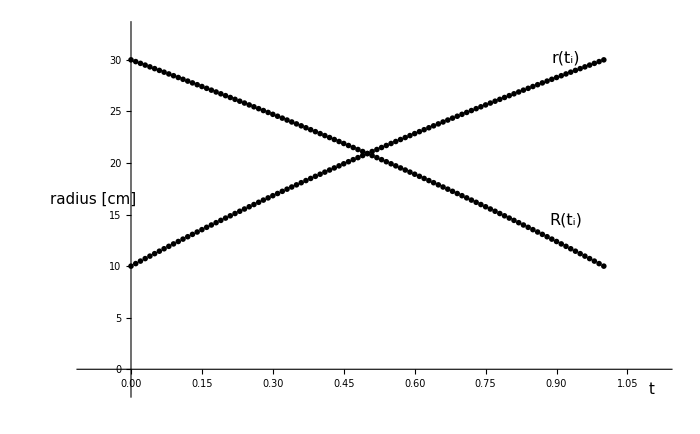

```mathematica
(* ::Section::*)(*Article-style Figure 4,matching Figure 2 style*)
ptsR4=Transpose[{tGrid4,rGrid4}];
ptsBigR4=Transpose[{tGrid4,RGrid4}];

fig4Article=Show[{ListPlot[ptsR4,PlotStyle->Directive[Black],PlotMarkers->{Automatic,0.012},Joined->False],ListPlot[ptsBigR4,PlotStyle->Directive[Black],PlotMarkers->{Automatic,0.012},Joined->False]},Axes->True,Frame->False,AxesOrigin->{0,0},AxesStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,12],PlotRange->{{-0.09,1.12},{-2,33}},ImageSize->700,AspectRatio->0.62,PlotRangePadding->Scaled[0.02],Epilog->{Inset[Style["r(t_i)",16,Black,Italic],{0.92,30.2}],Inset[Style["R(t_i)",16,Black,Italic],{0.92,14.5}],Inset[Style["t",15,Black,Italic],{1.1,-2}],Rotate[Inset[Style["radius [cm]",15,Black],{-0.08,16.5}],Pi/2]}];

fig4Article
```

```mathematica
Export[FileNameJoin[{outputRoot,"figures","Figure4_article_style.png"}],fig4Article,ImageResolution->300];

Export[FileNameJoin[{outputRoot,"figures","Figure4_article_style.pdf"}],fig4Article];
```

```mathematica
(* ::Section::*)(*Data for Figure 3:one symmetrization step*)
iFig3=30;
nFig3=paramsArticle["nGrid"];

ti=N[iFig3/nFig3];
tSym=N[1-ti];

tGrid3=mapDataArticle["tGrid"];
rGrid3=mapDataArticle["rGrid"];
RGrid3=mapDataArticle["RGrid"];

r1Curve=Transpose[{tGrid3,rGrid3}];
R1Curve=Transpose[{tGrid3,RGrid3}];

r1ti=rGrid3[[iFig3+1]];
R1ti=RGrid3[[iFig3+1]];

r1Sym=rGrid3[[nFig3-iFig3+1]];
R1Sym=RGrid3[[nFig3-iFig3+1]];

r2ti=(r1ti+R1Sym)/2;
r2Sym=(r1Sym+R1ti)/2;

Print["ti     = ",ti];
Print["1-ti   = ",tSym];
Print["r1(ti) = ",N[r1ti,10]];
Print["R1(ti) = ",N[R1ti,10]];
Print["r1(1-ti) = ",N[r1Sym,10]];
Print["R1(1-ti) = ",N[R1Sym,10]];
Print["r2(ti) = ",N[r2ti,10]];
Print["r2(1-ti) = ",N[r2Sym,10]];
```

ti     = 0.3

1-ti   = 0.7

r1(ti) = 16.

R1(ti) = 25.4269

r1(1-ti) = 24.

R1(1-ti) = 17.648

r2(ti) = 16.824

r2(1-ti) = 24.7134

```mathematica
(* ::Section::*)(*Labels for Figure 3*)tiSymb=Subscript[Style["t",Italic],"i"];
oneMinusTiSymb=Row[{"1-",Subscript[Style["t",Italic],"i"]}];

lblr1ti=Row[{Subscript[Style["r",Italic],1],"(",tiSymb,")"}];
lblR1ti=Row[{Subscript[Style["R",Italic],1],"(",tiSymb,")"}];

lblr1Sym=Row[{Subscript[Style["r",Italic],1],"(",oneMinusTiSymb,")"}];
lblR1Sym=Row[{Subscript[Style["R",Italic],1],"(",oneMinusTiSymb,")"}];

lblr2ti=Row[{Subscript[Style["r",Italic],2],"(",tiSymb,")"}];
lblr2Sym=Row[{Subscript[Style["r",Italic],2],"(",oneMinusTiSymb,")"}];

lblCurveRising=Row[{Subscript[Style["r",Italic],1],"(",Style["t",Italic],")"}];
lblCurveFalling=Row[{Subscript[Style["R",Italic],1],"(",Style["t",Italic],")"}];
```

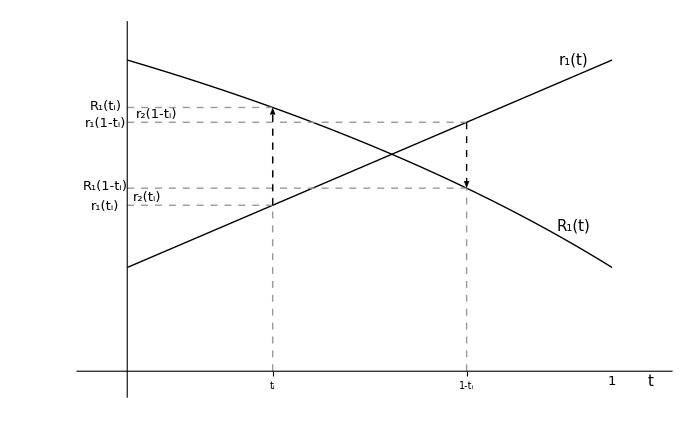

```mathematica
(* ::Section::*)(*Figure 3-- aligned with original diagram*)curveStyle=Directive[Black,AbsoluteThickness[1.0]];
guideStyle=Directive[GrayLevel[0.6],AbsoluteThickness[1],Dashed];
axisStyle=Directive[Black,AbsoluteThickness[0.8]];

xLeftLabel=-0.045;
xR2Label=0.06;

yLevels=Sort[{r1ti,R1Sym,r1Sym,R1ti,10,30}];
yLevelsUnique=DeleteDuplicates[Round[#,10^-8]&/@yLevels];

fig3ArticleFinal=Show[{ListLinePlot[r1Curve,PlotStyle->curveStyle,InterpolationOrder->1],ListLinePlot[R1Curve,PlotStyle->curveStyle,InterpolationOrder->1],Graphics[{guideStyle,(*horizontal dotted guides exactly as in original*)Line[{{0,R1ti},{ti,R1ti}}],Line[{{0,r1Sym},{1-ti,r1Sym}}],Line[{{0,R1Sym},{tSym,R1Sym}}],Line[{{0,r1ti},{ti,r1ti}}],
(*vertical dotted guides exactly as in original*)
Line[{{ti,0},{ti,R1ti}}],
Line[{{tSym,0},{tSym,R1Sym}}],Black,
(*small arrows only,no horizontal r2 guides*)
Arrowheads[0.02],
Arrow[{{ti,r1ti},{ti,R1ti}}],
Arrow[{{tSym,r1Sym},{tSym,R1Sym}}]}]},Axes->True,Frame->False,AxesOrigin->{0,0},AxesStyle->axisStyle,Ticks->{{{ti,Style["\!\(\*SubscriptBox[\(t\), \(i\)]\)",15,Black,Italic]},{tSym,Style["1-\!\(\*SubscriptBox[\(t\), \(i\)]\)",15,Black,Italic]}},({#,""}&/@DeleteDuplicates[Round[#,10^-8]&/@Sort[{r1ti,R1Sym,r2ti,r2Sym,r1Sym,R1ti}]])},PlotRange->{{-0.08,1.10},{-1.8,33}},PlotRangePadding->Scaled[0.02],ImageSize->700,AspectRatio->0.62,Epilog->{(*curve labels*)
Inset[Style["\!\(\*SubscriptBox[\(r\), \(1\)]\)(t)",15,Black,Italic],{0.92,30.0}],
Inset[Style["\!\(\*SubscriptBox[\(R\), \(1\)]\)(t)",15,Black,Italic],{0.92,14.0}],
(*x-axis labels*)
Inset[Style["1",13,Black],{1.0,-1.0}],
Inset[Style["t",15,Black,Italic],{1.08,-1.0}],
(*left-side labels*)
Inset[Style["\!\(\*SubscriptBox[\(R\), \(1\)]\)(\!\(\*SubscriptBox[\(t\), \(i\)]\))",13,Black,Italic],{xLeftLabel,R1ti+0.12}],Inset[Style["\!\(\*SubscriptBox[\(r\), \(1\)]\)(1-\!\(\*SubscriptBox[\(t\), \(i\)]\))",13,Black,Italic],{xLeftLabel,r1Sym-0.12}],Inset[Style["\!\(\*SubscriptBox[\(R\), \(1\)]\)(1-\!\(\*SubscriptBox[\(t\), \(i\)]\))",13,Black,Italic],{xLeftLabel,R1Sym+0.12}],Inset[Style["\!\(\*SubscriptBox[\(r\), \(1\)]\)(\!\(\*SubscriptBox[\(t\), \(i\)]\))",13,Black,Italic],{xLeftLabel,r1ti-0.12}],
(*r2 labels only,without guide lines*)
Inset[Style["\!\(\*SubscriptBox[\(r\), \(2\)]\)(1-\!\(\*SubscriptBox[\(t\), \(i\)]\))",13,Black,Italic],{xR2Label,r2Sym+0.05}],Inset[Style["\!\(\*SubscriptBox[\(r\), \(2\)]\)(\!\(\*SubscriptBox[\(t\), \(i\)]\))",13,Black,Italic],{xR2Label-0.018,r2ti-0.05}]}];

fig3ArticleFinal
```

```mathematica
Export[FileNameJoin[{outputRoot,"figures","Figure3_article_style_final.png"}],fig3ArticleFinal,ImageResolution->300];

Export[FileNameJoin[{outputRoot,"figures","Figure3_article_style_final.pdf"}],fig3ArticleFinal];
```

```mathematica
(* ::Section::*)(*Data for Figure 5*)If[!ValueQ[midArticle],midArticle=CVTPulley`Symmetrization`IterateMidpoint[paramsArticle,"StoreHistory"->False,"ImplicitStoreHistory"->False];];

If[!ValueQ[profilesArticle],symArticle=CVTPulley`Symmetrization`SymmetrizationData[paramsArticle,"StoreHistory"->False,"ImplicitStoreHistory"->False];
profilesArticle=CVTPulley`Symmetrization`BuildSymmetricDiscreteProfiles[symArticle];];

tGrid5=profilesArticle["tGrid"];
rGrid5=profilesArticle["rGrid"];
RGrid5=profilesArticle["RGrid"];

ptsR5=Transpose[{tGrid5,rGrid5}];
ptsBigR5=Transpose[{tGrid5,RGrid5}];

xi5=midArticle["Finalr"];

Tleft={0,paramsArticle["rMin"]};
Tmid={0.5,xi5};
Tright={1,paramsArticle["rMax"]};

TpLeft={0,paramsArticle["rMax"]};
TpMid={0.5,xi5};
TpRight={1,paramsArticle["rMin"]};

Print["xi = ",N[xi5,12]];
```

xi = 20.9158

```mathematica
(* ::Section::*)(*Quadratic approximations for Figure 5*)qRising[t_]=Expand@InterpolatingPolynomial[{Tleft,Tmid,Tright},t];
qFalling[t_]=Expand@InterpolatingPolynomial[{TpLeft,TpMid,TpRight},t];

qRisingData=Table[{t,qRising[t]},{t,0,1,0.005}];
qFallingData=Table[{t,qFalling[t]},{t,0,1,0.005}];

Print["qRising(t)  = ",qRising[t]];
Print["qFalling(t) = ",qFalling[t]];
```

qRising(t)  = 10.+23.6632 t-3.6632 t^2

qFalling(t) = 30.-16.3368 t-3.6632 t^2

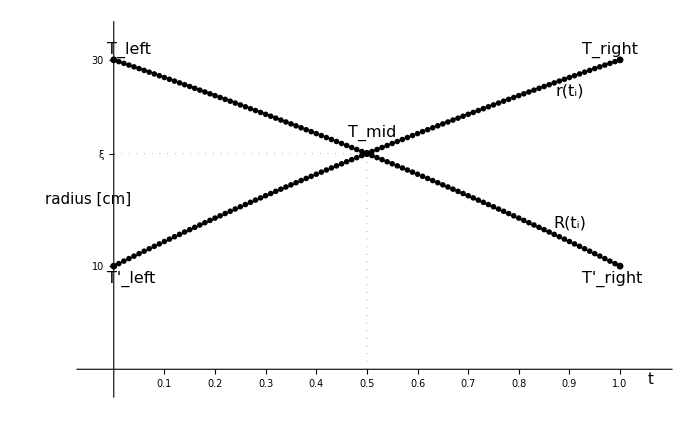

```mathematica
(* ::Section::*)(*Figure 5*)curveStyle=Directive[Black,AbsoluteThickness[0.9]];
guideStyle=Directive[GrayLevel[0.6],AbsoluteThickness[0.8],Dotted];
pointStyle=Directive[Black];
specialPointStyle=Directive[Black,PointSize[0.007]];

iterPointSizeR=0.01;
iterPointSizeBigR=0.01;

xTicks5=Table[{x,Style[NumberForm[x,{2,1}],13,Black]},{x,0.1,1.0,0.1}];

yTicks5={{10,Style["10",13,Black]},{xi5,Style["ξ",15,Black,Italic]},{30,Style["30",13,Black]}};

fig5Article=Show[{(*quadratic approximations*)ListLinePlot[qRisingData,PlotStyle->curveStyle,InterpolationOrder->1],ListLinePlot[qFallingData,PlotStyle->curveStyle,InterpolationOrder->1],(*discrete iterated profiles*)ListPlot[ptsR5,PlotStyle->pointStyle,PlotMarkers->{Automatic,iterPointSizeR},Joined->False],ListPlot[ptsBigR5,PlotStyle->pointStyle,PlotMarkers->{Automatic,iterPointSizeBigR},Joined->False],Graphics[{guideStyle,(*Tmid coordinate guides*)Line[{{0,xi5},{0.5,xi5}}],Line[{{0.5,0},{0.5,xi5}}],(*highlighted defining points*)specialPointStyle,Point[Tleft],Point[Tmid],Point[Tright],Point[TpLeft],Point[TpMid],Point[TpRight]}]},Axes->True,Frame->False,AxesOrigin->{0,0},AxesStyle->Directive[Black,AbsoluteThickness[0.8]],Ticks->{xTicks5,yTicks5},PlotRange->{{-0.05,1.08},{-2,33}},PlotRangePadding->Scaled[0.02],ImageSize->700,AspectRatio->0.62,Epilog->{(*curve labels*)Inset[Style["r(\!\(\*SubscriptBox[\(t\), \(i\)]\))",16,Black,Italic],{0.90,27}],Inset[Style["R(\!\(\*SubscriptBox[\(t\), \(i\)]\))",16,Black,Italic],{0.90,14.2}],(*special point labels*)Inset[Style["\!\(\*SubscriptBox[\(T\), \(left\)]\)",16,Black,Italic],{0.03,31}],Inset[Style["\!\(\*SubscriptBox[\(T\), \(mid\)]\)",16,Black,Italic],{0.51,xi5+2}],Inset[Style["\!\(\*SubscriptBox[\(T\), \(right\)]\)",16,Black,Italic],{0.98,31}],Inset[Style["T'_left",16,Black,Italic],{0.035,8.8}],Inset[Style["T'_right",16,Black,Italic],{0.985,8.8}],(*axis labels*)Inset[Style["t",15,Black,Italic],{1.06,-1.0}],Rotate[Inset[Style["radius [cm]",15,Black],{-0.05,16.5}],Pi/2]}];

fig5Article
```

```mathematica
Export[FileNameJoin[{outputRoot,"figures","Figure5_article_style_final.png"}],fig5Article,ImageResolution->300];

Export[FileNameJoin[{outputRoot,"figures","Figure5_article_style_final.pdf"}],fig5Article];
```

```mathematica
(* ::Section::*)(*Data for Figure 6:belt-length deviation of quadratic approximation*)L0Fig6=paramsArticle["beltLength"];

fr[t_]:=qRising[t];
fR[t_]:=qFalling[t];

beltErr[t_]:=CVTPulley`BeltLength`BeltLength[fr[t],fR[t],paramsArticle["d"]]-L0Fig6;

deltaPct[t_]:=100.0*beltErr[t]/L0Fig6;
```

```mathematica
(* ::Section::*)(*Sampling the deviation profile*)devData6=Table[{t,deltaPct[t]},{t,0,1,0.005}];

Print["Min deviation [%] = ",N[Min[devData6[[All,2]]],12]];
Print["Max deviation [%] = ",N[Max[devData6[[All,2]]],12]];
```

Min deviation [%] = -0.00371806

Max deviation [%] = 2.09431×10^-14

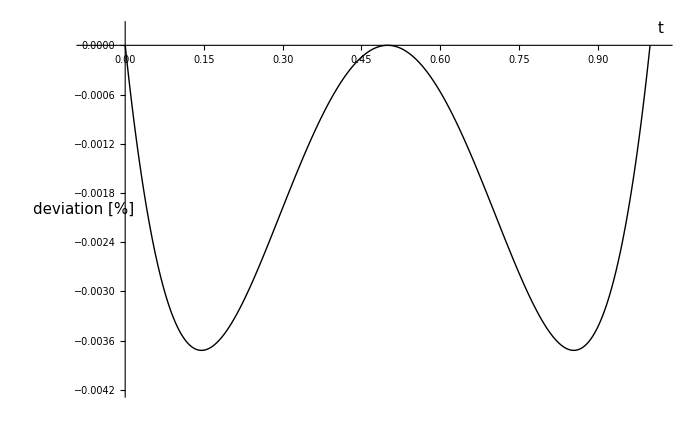

```mathematica
(* ::Section::*)(*Figure 6-- final version with manual axis labels*)fig6Article=Show[{ListLinePlot[devData6,PlotStyle->Directive[Black,AbsoluteThickness[1.0]],InterpolationOrder->3]},Axes->True,Frame->False,AxesOrigin->{0,0},AxesStyle->Directive[Black,AbsoluteThickness[0.8]],TicksStyle->Directive[Black,12],PlotRange->{{-0.07,1.02},{-0.0042,0.0002}},PlotRangePadding->Scaled[0.02],ImageSize->700,AspectRatio->0.62,Epilog->{Inset[Style["t",15,Black,Italic],{1.02,0.0002}],Rotate[Inset[Style["deviation [%]",15,Black],{-0.08,-0.002}],Pi/2]}];

fig6Article
```

```mathematica
Export[FileNameJoin[{outputRoot,"figures","Figure6_article_style.png"}],fig6Article,ImageResolution->300];

Export[FileNameJoin[{outputRoot,"figures","Figure6_article_style.pdf"}],fig6Article];
```